## The condition of priority effects (c11=c22, c12=c21,w11=w22, w12=w21)

### Parameters

```mathematica
(* consumption rate of species 1 & 2 *)
c11=.;c22=c11;c12=0.1;c21=c12;
(* conversion efficiency of species 1 & 2 *)
w11 =.;w22 = w11;w12 =0.1;w21 =w12;
(* mortality rate of species 1 & 2 *)
m1=0.5;m2=0.5;
(* growth ratey of resources *)
r1=10;r2=10;
(* carrying capacity of resources *)
K1=100;K2=100;
```

### Coefficient of competition

```mathematica
B1=c11 K1 w11;
B2=c12 K2 w12;
B3=c21 K1 w21;
B4=c22 K2 w22;

alpha11=(c11/r1 B1+c12/r2 B2)/(B1+B2-m1);
alpha12=(c21/r1 B1+c22/r2 B2)/(B1+B2-m1);
alpha21=(c11/r1 B3 +c12/r2 B4)/(B3+B4-m2);
alpha22=(c21/r1 B3 +c22/r2 B4)/(B3+B4-m2);
```

### Niche overlap

```mathematica
no=Sqrt[(alpha12 alpha21)/(alpha11 alpha22)];
```

### Phase diagram

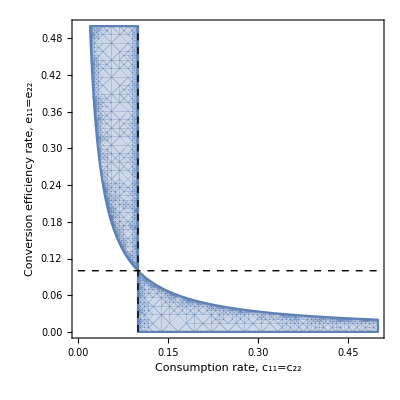

```mathematica
Show[RegionPlot[1<no,{c11,0,0.5},{w11,0,0.5},PlotPoints->10,MaxRecursion->8,Method->{"TransparentPolygonMesh"->True}],
Graphics[{Black,Dashed,Thick,Line[{{0.1,0},{0.1,0.5}}]}],
Graphics[{Black,Dashed,Thick,Line[{{0.,0.1},{0.5,0.1}}]}],FrameLabel->{{RawBoxes[RowBox[{RowBox[{"Conversion"," ","efficiency"," ","rate"}],","," ",RowBox[{SubscriptBox[StyleBox["e",FontSlant->"Italic"],"11"],"=",SubscriptBox[StyleBox["e",FontSlant->"Italic"],"22"]}]}]],None},{RawBoxes[RowBox[{RowBox[{"Consumption"," ","rate"}],","," ",RowBox[{SubscriptBox[StyleBox["c",FontSlant->"Italic"],"11"],"=",SubscriptBox[StyleBox["c",FontSlant->"Italic"],"22"]}]}]],None}},PlotLabel->None,LabelStyle->{FontFamily->"Arial",18,GrayLevel[0]}
]
```